```mathematica
s[t_]:=1/(1+ⅇ^(-t));
y[t_,w_,b_]:=s[(t+w/2)/b]-s[(t-w/2)/b];
```

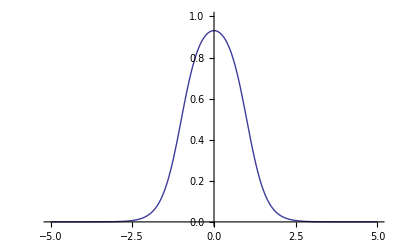

```mathematica
sampleWidth=3;
samplePeriod=0.01;
w=2;
b=0.3;
Plot[y[t,w,b],{t,-5,5},PlotRange->{{-5,5},{0,1}}]
(* y is symmetric; sample half the domain *)
stepLut=Table[y[t,w,b],{t,0,sampleWidth,sampleWidth*samplePeriod}];
(* Duplicate the last point to make the LUT easier to work with *)
stepLut=Join[stepLut,{stepLut[[-1]]}];
```

```mathematica
stepLutJs="step_lut_sample_period="<>ToString[samplePeriod]<>";\n"<>
"step_lut_sample_n="<>ToString[N[Ceiling[1/samplePeriod + 1]]]<>";\n"<>
"step_lut_sample_width="<>ToString[sampleWidth]<>";\n"<>
"step_lut="<>RoundedJsList[stepLut,0.001]<>";\n";
```

```mathematica
Export["/home/xcolwell/step_lut.js",stepLutJs,"Text"]
```

/home/xcolwell/step_lut.js

```mathematica
RoundedJsList[ns_,p_]:=Block[{d},
d=Ceiling[Log[10,1/p]];
StringReplace[
StringReplace[ToString[Round[ns,p],InputForm],
RegularExpression["(\\d*)\\.(\\d{0,"<>ToString[d]<>"})(\\d*)"]->"$1.$2"],
{"{"->"[","}"->"]"}]
]
```

```mathematica
Js[str_]:=
StringReplace[StringReplace[str,{"{"->"[","}"->"]"}],
{
RegularExpression["([^\\[\\]\",]+)\\s*->"]->"\"$1\":",
RegularExpression["->"]->":",
RegularExpression["\\[\\s*JSMAP\\s*,?"]->"{",
RegularExpression[",?\\s*JSMAP\\s*\\]"]->"}"
}
];
```